```mathematica
SetDirectory[NotebookDirectory[]]
Import[NotebookDirectory[]<>"library_quantumInformation.m"]
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

/Users/alexanderpickston/Dropbox (Heriot-Watt University Team)/RES_EPS_EMQL/userFolders/Alex/sim_notebooks/model_graphStates

# Graphs

Styling the output of the Graphs we obtain the correct indices for the vertices and a nice way to represent the outputs of LC and any following operations. Using the ketState from the output of the

### Initial styling definitions to add to library

```mathematica
{g=-Graphics-;h=-Graphics-;}
```

{Null}

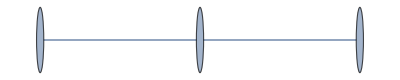

```mathematica
TreeGraph[{1,2,3},{1<->2,2<->3}]
```

```mathematica
FindLUequivalent[-Graphics-]
```

FindLUequivalent[-Graphics-]

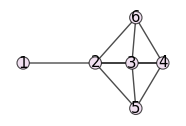
```mathematica
GraphPlot3D[-Graphics-,EdgeStyle->Directive[Black,Thickness[.001]],VertexStyle->Directive[EdgeForm[{Thick,Gray}],Darker@Darker@Gray],VertexLabelStyle->Directive[White,FontFamily->"YuMincho",25]]
```

-Graphics3D-

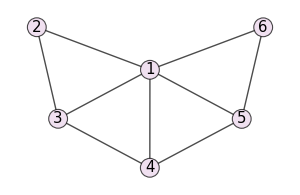

```mathematica
GraphUnion[g,h,

VertexShapeFunction->"Circle",
VertexSize->Medium,
VertexStyle->Directive[EdgeForm[{Thick,Black}],LightPurple],
EdgeStyle->Directive[Black,Thick],
VertexLabels->Placed["Name",{1/2,1/2}],
VertexLabelStyle->Directive[Black,FontFamily->"YuMincho",15]
,ImageSize->300

]
```

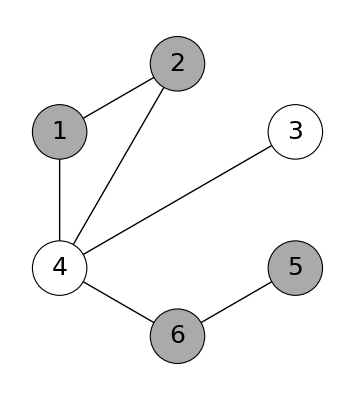

### Testing with functions from library

```mathematica
ketState={{1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)}};
```

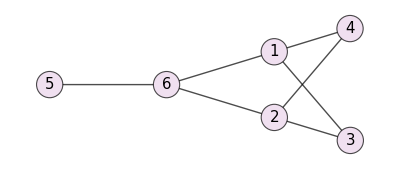
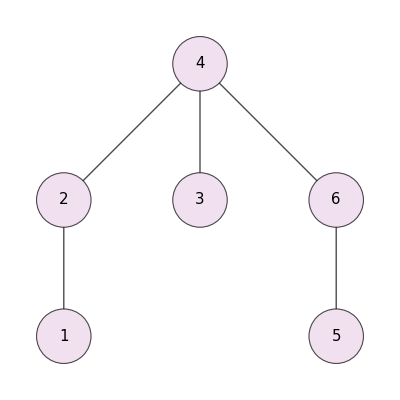

```mathematica
graphsFromKet=DeleteDuplicates[DrawGraphFromStab/@FindGraphFromXZStab[ketState],IsomorphicGraphQ]
```

There are many ways to get from the trident to 2-party QKD between users. We should try to explore all of the ways we can get from the trident to Bell states.

### Trident to n-party QKD

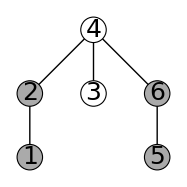

```mathematica
graphStyle@FindLUequivalent[-Graphics-,3]
```

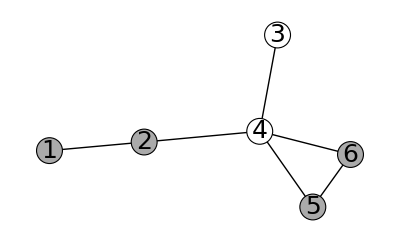

```mathematica
graphStyle@FindLUequivalent[-Graphics-,6]
```

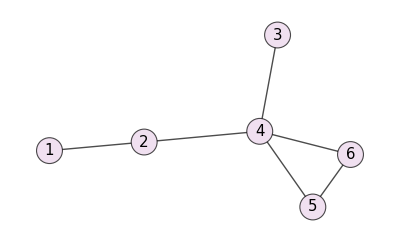
```mathematica
graphStyle@FindLUequivalent[-Graphics-,4]
```

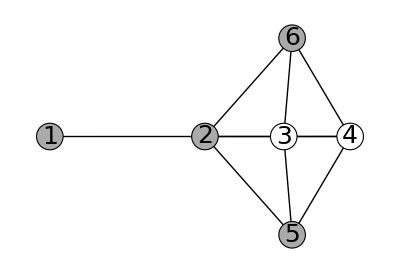

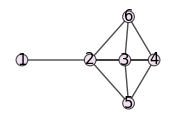
```mathematica
(*LayeredGraphPlot[-Graphics-]*)
```

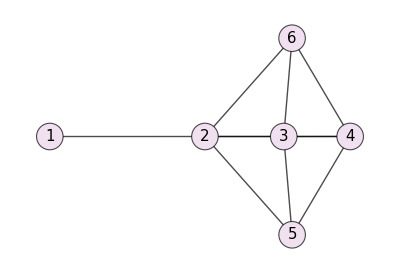
```mathematica
graphStyle@Zmeasurement[-Graphics-,3]
```

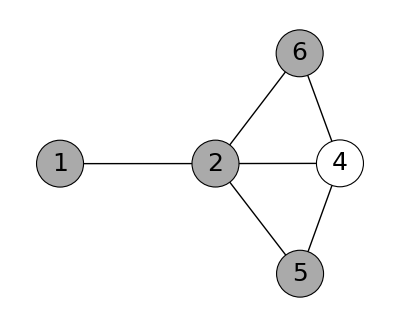

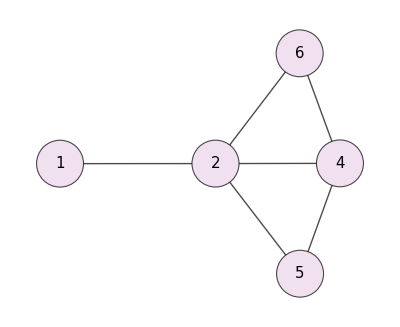
```mathematica
graphStyle@Zmeasurement[-Graphics-,4]
```

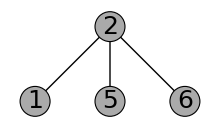

```mathematica
{Zmeasurement[%,1],Zmeasurement[%,2],Zmeasurement[%,5],Zmeasurement[%,6]}
```

EdgeList::argt: EdgeList called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of EdgeList::argt will be suppressed during this calculation.

{Graph[EdgeList[],VertexShapeFunction→Circle,VertexSize→0.4,VertexStyle→Directive[EdgeForm[{Thickness[Large],GrayLevel[0]}],RGBColor[0.94, 0.88, 0.94]],EdgeStyle→Directive[GrayLevel[0],Thickness[Large]],VertexLabels→Placed[Name,{1/2,1/2}],VertexLabelStyle→Directive[GrayLevel[0],FontFamily→YuMincho,15],VertexSize→0.4],Graph[EdgeList[],VertexShapeFunction→Circle,VertexSize→0.4,VertexStyle→Directive[EdgeForm[{Thickness[Large],GrayLevel[0]}],RGBColor[0.94, 0.88, 0.94]],EdgeStyle→Directive[GrayLevel[0],Thickness[Large]],VertexLabels→Placed[Name,{1/2,1/2}],VertexLabelStyle→Directive[GrayLevel[0],FontFamily→YuMincho,15],VertexSize→0.4],Graph[EdgeList[],VertexShapeFunction→Circle,VertexSize→0.4,VertexStyle→Directive[EdgeForm[{Thickness[Large],GrayLevel[0]}],RGBColor[0.94, 0.88, 0.94]],EdgeStyle→Directive[GrayLevel[0],Thickness[Large]],VertexLabels→Placed[Name,{1/2,1/2}],VertexLabelStyle→Directive[GrayLevel[0],FontFamily→YuMincho,15],VertexSize→0.4],Graph[EdgeList[],VertexShapeFunction→Circle,VertexSize→0.4,VertexStyle→Directive[EdgeForm[{Thickness[Large],GrayLevel[0]}],RGBColor[0.94, 0.88, 0.94]],EdgeStyle→Directive[GrayLevel[0],Thickness[Large]],VertexLabels→Placed[Name,{1/2,1/2}],VertexLabelStyle→Directive[GrayLevel[0],FontFamily→YuMincho,15],VertexSize→0.4]}

#### Quick test of the library function

Testing the libraries integrated function

```mathematica
Module[{subGraph,diffGraph,complementGraph,out},FindLUequivalent[graph_,vertex_]:=((*Select the subgraph generated by the vertex and its neighbours*)subGraph=Subgraph[graph,AdjacencyList[graph,vertex]];
(*Complement the sub graph*)complementGraph=GraphComplement[subGraph];
(*remove the starting subgraph*)diffGraph=GraphDifference[graph,subGraph];
(*Union the new subGraph with the remaining main graph*)out=GraphUnion[diffGraph,complementGraph,VertexShapeFunction->"Circle",VertexStyle->Directive[EdgeForm[{Thick,Black}],LightPurple],EdgeStyle->Directive[Black,Thick],VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[Black,FontFamily->"YuMincho",15],VertexSize->0.4];
(*return the LC-equivalent graph*)Return[out];);];
```

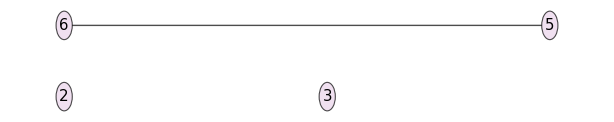

```mathematica
Subgraph[-Graphics-,AdjacencyList[-Graphics-,4]]
```

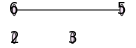
```mathematica
GraphComplement[-Graphics-]
```

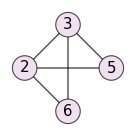

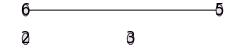
```mathematica
GraphDifference[-Graphics-,-Graphics-]
```

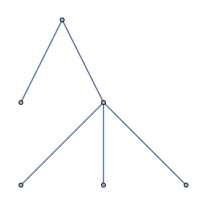

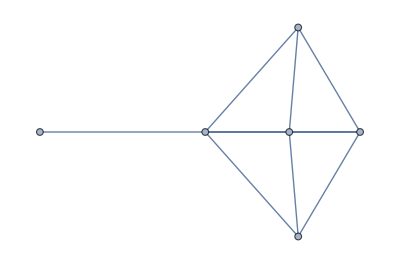

```mathematica
GraphUnion[-Graphics-,-Graphics-]
```

### Trident to 2-party QKD

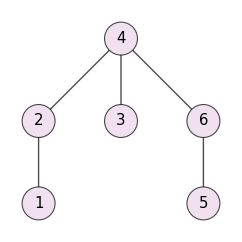

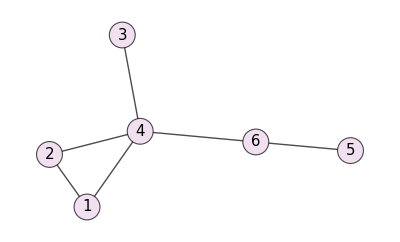

```mathematica
FindLUequivalent[-Graphics-,2]
```

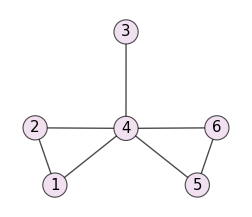

```mathematica
FindLUequivalent[%,6]
```

Almost a fully connected Graph

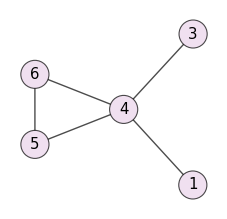

```mathematica
Zmeasurement[%,2]
```

Measuring X rather than Z. The issue is that the code that implements the X measurement randomly chooses the neighbour qubit. The neighbour qubit is crucial as the vertices that were joined to the vertex will be joined to the neighbour. If we measure Y on qubit 4 we get two Bell states.

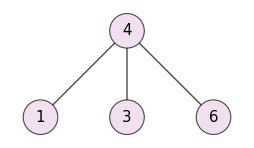

```mathematica
Zmeasurement[%,5]
```

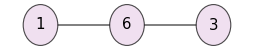

```mathematica
Xmeasurement[%,4]
```

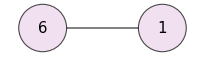

```mathematica
Zmeasurement[%,3]
```

### Trident to 2 pairs of Bell states

```mathematica
FindLUequivalent[-Graphics-,6]
```

-Graphics-

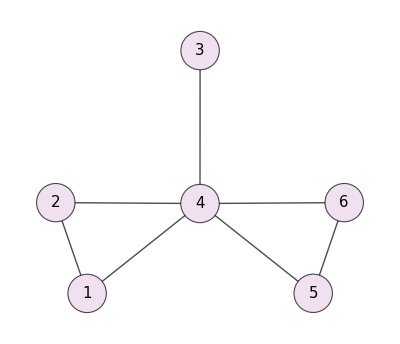

```mathematica
FindLUequivalent[%,2]
```

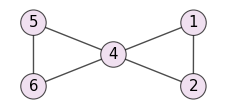

```mathematica
Zmeasurement[%,3]
```

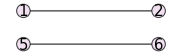

```mathematica
Zmeasurement[%,4]
```

### Trident to 2 pairs of Bell states

```mathematica
FindLUequivalent[-Graphics-,6]
```

-Graphics-

```mathematica
FindLUequivalent[%,2]
```

-Graphics-

```mathematica
Zmeasurement[%,3]
```

-Graphics-

```mathematica
Zmeasurement[%,4]
```

-Graphics-

### Trident to 2 pairs of Bell states - MOST RECENT

```mathematica
rocketColors
```

{RGBColor[Rational[37, 256], Rational[25, 256], Rational[7, 32]],RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[1, 2], Rational[57, 256], Rational[13, 32]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]],RGBColor[Rational[103, 128], Rational[73, 256], Rational[47, 128]],RGBColor[Rational[57, 64], Rational[119, 256], Rational[45, 128]],RGBColor[Rational[241, 256], Rational[199, 256], Rational[85, 128]],RGBColor[Rational[31, 32], Rational[233, 256], Rational[55, 64]]}

```mathematica
userColor=Lighter@Gray;
networkColor=White;
thickness=Thickness[.005];
```

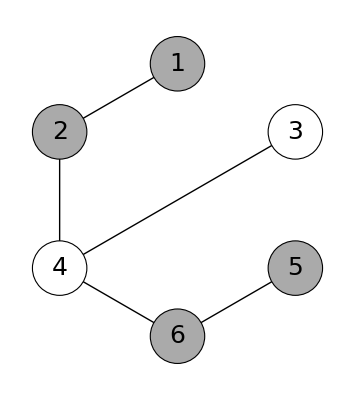

```mathematica
CustomGraphStyle[graph_]:=Graph[graph,
VertexStyle->{
1->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],
2->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],
5->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],
6->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],
4->Directive[EdgeForm[{Thick,Opacity[1],Black}],networkColor],
3->Directive[EdgeForm[{Thick,Opacity[1],Black}],networkColor]},
VertexLabelStyle->Directive[Black,FontFamily->"IBM Plex Sans",25],
EdgeStyle->Directive[Black,Thick,Opacity[1]],
(*VertexCoordinates->{{3,2},{2,0},{3,4},{5,5},{1,3},{0,1}}*)
GraphLayout->"CircularEmbedding"]
CustomGraphStyle@-Graphics-
```

```mathematica
CustomGraphStyle@FindLUequivalent[-Graphics-,2]
```

-Graphics-

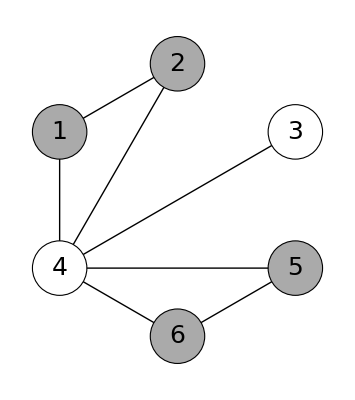

```mathematica
CustomGraphStyle@FindLUequivalent[-Graphics-,6]
```

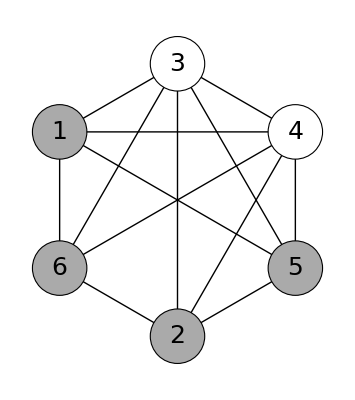

```mathematica
CustomGraphStyle@FindLUequivalent[-Graphics-,4]
```

#### 1, 2 and 5, 6

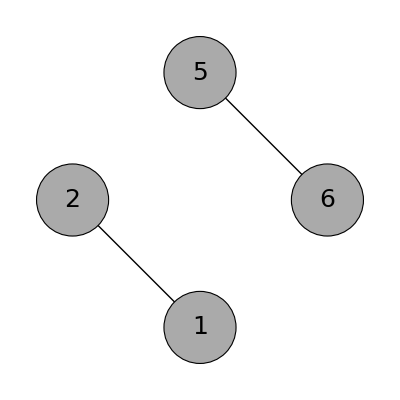

```mathematica
CustomGraphStyle@Zmeasurement[-Graphics-,4]
```

#### 1, 2

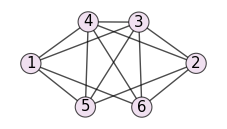
```mathematica
CustomGraphStyle@Zmeasurement[-Graphics-,3]
```

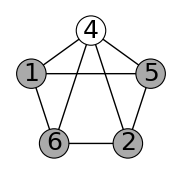

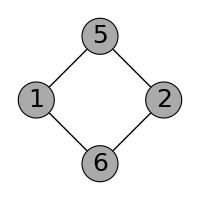

```mathematica
CustomGraphStyle@Zmeasurement[%,4]
```

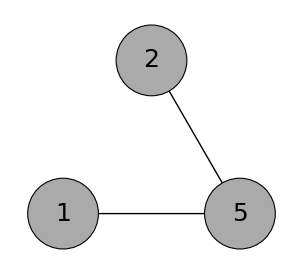

```mathematica
CustomGraphStyle@Zmeasurement[%,6]
```

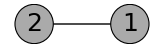

```mathematica
CustomGraphStyle@Xmeasurement[%,5]
```

#### 1,6

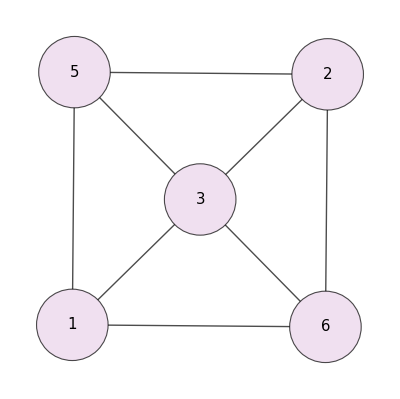

```mathematica
Zmeasurement[-Graphics-,4]
```

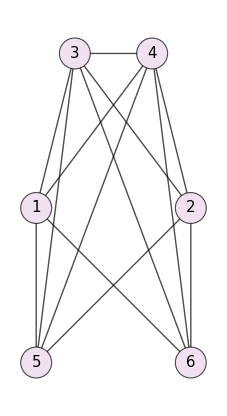

```mathematica
Graph[-Graphics-,
VertexCoordinates->{{0,2},{2,2},{0.5,4},{1.5,4},{0,0},{2,0}}]
```

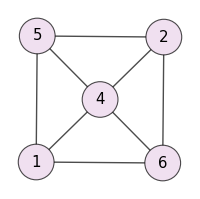

```mathematica
Zmeasurement[%,3]
```

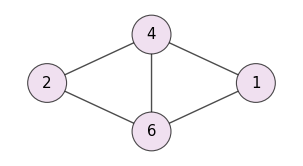

```mathematica
Zmeasurement[%,5]
```

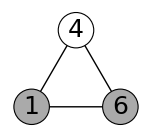

```mathematica
graphStyle@Zmeasurement[%,2]
```

#### 1,5

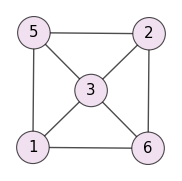

```mathematica
Zmeasurement[-Graphics-,4]
```

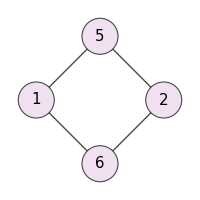

```mathematica
Zmeasurement[%,3]
```

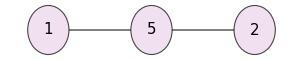

```mathematica
Zmeasurement[%,6]
```

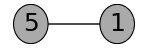

```mathematica
graphStyle@Zmeasurement[%,2]
```

#### 2,5

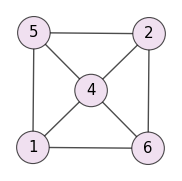

```mathematica
Zmeasurement[-Graphics-,3]
```

```mathematica
Zmeasurement[%,4]
```

-Graphics-

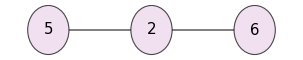

```mathematica
Zmeasurement[%,1]
```

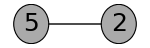

```mathematica
graphStyle@Zmeasurement[%,6]
```

#### 2,6

```mathematica
Zmeasurement[-Graphics-,3]
```

-Graphics-

```mathematica
Zmeasurement[%,4]
```

-Graphics-

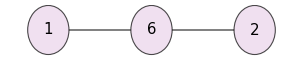

```mathematica
Zmeasurement[%,5]
```

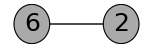

```mathematica
graphStyle@Zmeasurement[%,1]
```

#### 5, 6

```mathematica
Zmeasurement[-Graphics-,3]
```

-Graphics-

```mathematica
Zmeasurement[%,4]
```

-Graphics-

```mathematica
Zmeasurement[%,1]
```

-Graphics-

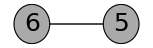

```mathematica
graphStyle@Xmeasurement[%,2]
```

### Trident to 2 pairs of Bell states

```mathematica
FindLUequivalent[-Graphics-,6]
```

-Graphics-

```mathematica
FindLUequivalent[%,2]
```

-Graphics-

```mathematica
FindLUequivalent[%,4]
```

-Graphics-

```mathematica
Zmeasurement[%,4]
```

-Graphics-

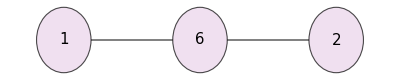

```mathematica
Zmeasurement[%,5]
```

### All outcomes from Trident

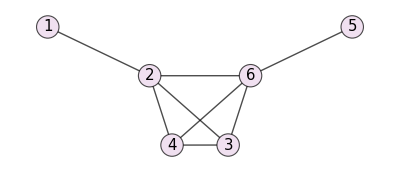
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
step1=FindLUequivalent[-Graphics-,#]&/@{1,2,3,4,5,6}
```

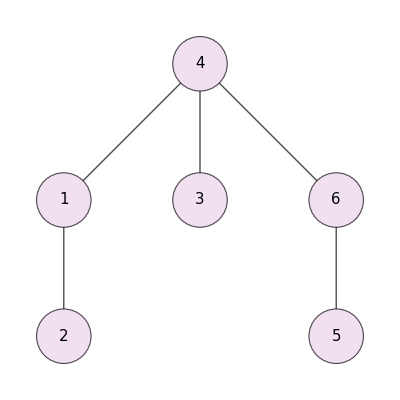
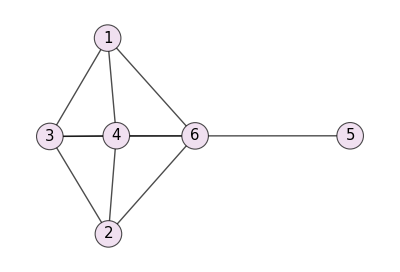
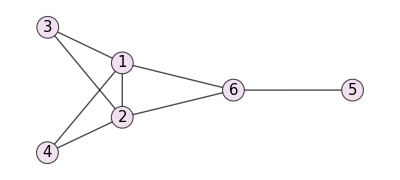
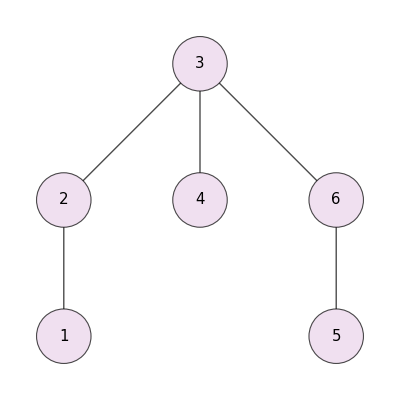
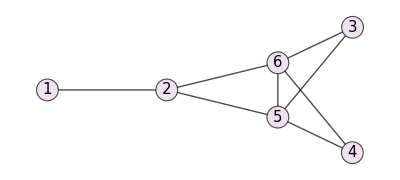
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
step2=Table[FindLUequivalent[#,i],{i,1,6}]&/@step1
```

```mathematica
step3=Table[FindLUequivalent[#,i],{i,1,6}]&/@Flatten@step2
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

#### Z operation

```mathematica
step4=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step3;
DeleteDuplicates[Flatten@step4,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Z operation to step 4

```mathematica
step5=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step4;
DeleteDuplicates[Flatten@step5,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Z operation to step 5

```mathematica
step6=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step5;
DeleteDuplicates[Flatten@step6,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
step7=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step6;
DeleteDuplicates[Flatten@step7,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### All outcomes from Rocket

```mathematica
step1=FindLUequivalent[-Graphics-,#]&/@{1,2,3,4,5,6};
DeleteDuplicates[step1,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
step2=Table[FindLUequivalent[#,i],{i,1,6}]&/@step1;
DeleteDuplicates[Flatten@step2,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
step3=Table[FindLUequivalent[#,i],{i,1,6}]&/@Flatten@step2;
DeleteDuplicates[Flatten@step3,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Z operation

```mathematica
Length[DeleteDuplicates[Flatten@step4,IsomorphicGraphQ]]
```

21

```mathematica
{{step4noDuplicates⟦;;7⟧},step4noDuplicates⟦8;;14⟧,step4noDuplicates⟦15;;21⟧}
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
step4=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step3;
step4noDuplicates=DeleteDuplicates[Flatten@step4,IsomorphicGraphQ];
GraphicsGrid[{step4noDuplicates⟦;;7⟧,step4noDuplicates⟦8;;14⟧,step4noDuplicates⟦15;;21⟧}]
```

#### Z operation to step 4

```mathematica
step5=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step4;
DeleteDuplicates[Flatten@step5,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Z operation to step 5

```mathematica
step6=Table[Zmeasurement[#,i],{i,1,6}]&/@Flatten@step5;
DeleteDuplicates[Flatten@step6,IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Test

```mathematica
Ymeasurement[-Graphics-,4]
```

-Graphics-